## General Challenge

#### Game tree sketch

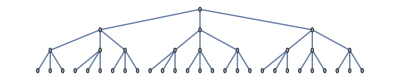

```mathematica
CompleteKaryTree[4,3,
GraphLayout->"LayeredDigraphEmbedding"]
```

## Utility Function

#### Utility BW1

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25|>];SpacedRow[{AddCaption[ShowPowerStructure[PowerStructure[{2,1,1,1,1},IdentityMatrix[5]],<|"focal"->{1},"circular"->True,"size"->{60,60}|>],"Better"],AddCaption[ShowPowerStructure[PowerStructure[{1,1,1,1,1},IdentityMatrix[5]],<|"focal"->{1},"circular"->True,"size"->{60,60}|>],"Worse"]},50]
```

-Graphics-
Better-Graphics-
Worse

#### Utility BW2

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.8,"α"->2.25|>];SpacedRow[{
AddCaption[ShowPowerStructure[PowerStructure[{1,1,1},IdentityMatrix[3]],<|"focal"->{1},"circular"->True,"size"->{50,50}|>],"Better"],
AddCaption[ShowPowerStructure[PowerStructure[{1,2,1},IdentityMatrix[3]],<|"focal"->{1},"circular"->True,"size"->{50,50}|>],"Worse"],
AddCaption[ShowPowerStructure[PowerStructure[{1,3,1},IdentityMatrix[3]],<|"focal"->{1},"circular"->True,"size"->{50,50}|>],"Even worse"]
},50]
```

-Graphics-
Better-Graphics-
Worse-Graphics-
Even worse

#### Utility BW3

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25|>];SpacedRow[{AddCaption[ShowPowerStructure[PowerStructure[{1,1,1,1,1,1},IdentityMatrix[6]],<|"focal"->{1},"circular"->True,"size"->{60,60}|>],"Better"],AddCaption[ShowPowerStructure[PowerStructure[{.6,Sqrt[5]},IdentityMatrix[2]],<|"focal"->{1},"circular"->True,"size"->{70,70}|>],"Worse"]},50]
```

-Graphics-
Better-Graphics-
Worse

#### Utility BW4

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25|>];AddCaption[ShowPowerStructure[PowerStructure[{9,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}/2,IdentityMatrix[16]],<|"focal"->{1},"circular"->True,"size"->{70,70}|>],"Great"]
```

-Graphics-
Great

#### Utility vectors

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25|>];f[ps_]:=AddCaption[ShowPowerStructure[ps,<|"labels"->False,"circular"->True,"size"->{50,50}|>],Column[{
"s = "<>ToString[ps["s"]],
"u = "<>ToString[Round[PrinceRank[ps],.01]]
},Alignment->Center]];
show=SpacedRow[Map[f,{
PowerStructure[{1,1,.5},IdentityMatrix[3]],
PowerStructure[{1,.5,.5},IdentityMatrix[3]],
PowerStructure[{1,.5,0},IdentityMatrix[3]],
PowerStructure[{1,0,0},IdentityMatrix[3]]
}],25]
Clear[f];
```

-Graphics-
s = {1., 1., 0.5}
u = {0.26, 0.26, 0.05}-Graphics-
s = {1., 0.5, 0.5}
u = {0.39, 0.08, 0.08}-Graphics-
s = {1., 0.5, 0.}
u = {0.47, 0.1, 0.}-Graphics-
s = {1., 0., 0.}
u = {0.59, 0., 0.}

#### Utility market share

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25|>];f[ps_]:=AddCaption[ShowPowerStructure[ps,<|"labels"->False,"circular"->True,"size"->{60,60},"focal"->{1}|>],Column[{
"%ms = "<>ToString[Round[ps["s"]/Total[ps["s"]],.01]],
"u = "<>ToString[Round[PrinceRank[ps],.01]]
},Alignment->Center]];
show=SpacedRow[Map[f,{
PowerStructure[{1,1,1,1},IdentityMatrix[4]],
PowerStructure[{1,3},IdentityMatrix[2]]
}],25]
Clear[f];
```

-Graphics-
%ms = {0.25, 0.25, 0.25, 0.25}
u = {0.15, 0.15, 0.15, 0.15}-Graphics-
%ms = {0.25, 0.75}
u = {0.06, 0.69}

#### Utility as function of s

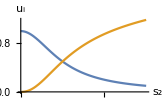
-Graphics-
Utility of two agents when s_1=1 and s_2 varies

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25|>];AddCaption[Plot[{Utility[{1.,x}][[1]],Utility[{1.,x}][[2]]},{x,0,3},PlotLegends->{"u_1","u_2"},AxesLabel->{"s_2","u_i"},ImageSize->{300,200}/1.8],"Utility of two agents when s_1=1 and s_2 varies"]
```

## Definition of PrinceRank

#### PR vs utility

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.8,"α"->2.25|>];f[T_]:=ShowPowerStructure[PowerStructure[{1,1,1,1,1},NormalizeTernaryT[T]],<|"circular"->True,"size"->{60,60}|>];
show=SpacedRow[{
f[IdentityMatrix[5]],f[({{0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}, {1, 1, 0, 1, 1}, {0, 0, 1, 0, 0}, {0, 0, 1, 0, 0}})],f[({{0, 0, -1, 0, 0}, {0, 0, -1, 0, 0}, {-1, -1, 0, -1, -1}, {0, 0, -1, 0, 0}, {0, 0, -1, 0, 0}})],f[RandomTernaryT[5,4,.2]]
},25]
Clear[f];
```

-Graphics--Graphics--Graphics--Graphics-

#### PR color spectrum

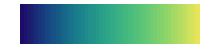
-Graphics-
Worse                                                         Better

```mathematica
AddCaption[MatrixPlot[{Map[ColorData["BlueGreenYellow"],Range[50]/50.],Map[ColorData["BlueGreenYellow"],Range[50]/50.]},Frame->None],"Worse                                                         Better"]
```

#### PR 3 charts

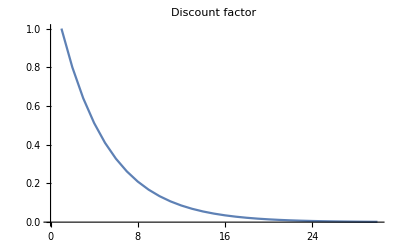
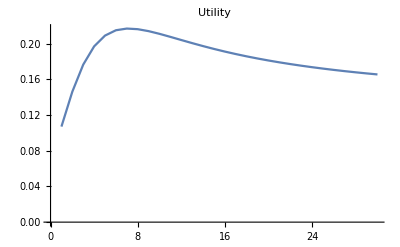
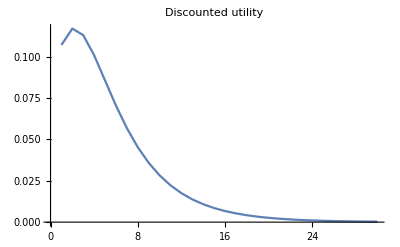

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25|>];ut=First[Transpose[Map[Utility[#s]&,SimulateLawOfMotion[RandomTernaryPowerStructure[5]]]]];
disc=Table[.8^t,{t,0,29}];
SpacedRow[{
ListLinePlot[disc,PlotLabel->Caption["Discount factor"],Ticks->None],
ListLinePlot[ut,PlotLabel->Caption["Utility"],Ticks->None],
ListLinePlot[disc*ut,PlotLabel->Caption["Discounted utility"],Ticks->None]
},25]
```

#### PR 3D

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->10|>];AddCaption[Plot3D[{
PrinceRank[PowerStructure[{1,1},{{1-Abs[y],x},{y,1-Abs[x]}}]][[1]],
PrinceRank[PowerStructure[{1,1},{{1-Abs[y],x},{y,1-Abs[x]}}]][[2]]
},{x,-1,1},{y,-1,1},
AxesLabel->{"T_(2,1)","T_(1,2)","PrinceRank"},Ticks->{{-1,0,1},{-1,0,1},None},ImageSize->{300,200}], 
"PrinceRank as a function of T where s={1,1}"]
```

-Graphics3D-
PrinceRank as a function of T where s={1,1}

## Implications of PrinceRank

#### IPR ideal

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];ShowPowerStructure[PowerStructure[{1,1,1,1},({{.97, .1, .1, .1}, {.01, .9, 0, 0}, {.01, 0, .9, 0}, {.01, 0, 0, .9}})],<|"focal"-> {1},"ternary"->False,"circular"->True,"size"->{75,75}|>]
```

-Graphics-

#### IPR asymmetric

```mathematica
ShowPowerStructure[PowerStructure[{1,1,1},NormalizeTernaryT[({{0, 0, 0}, {1, 0, 1}, {0, 0, 0}})]],<|"ternary"->False,"circular"->True,"focal"->{2},"size"->{60,60}|>]
```

-Graphics-

#### IPR symmetrized

```mathematica
ShowPowerStructure[PowerStructure[{1.,1.,1.},NormalizeTernaryT[SymmetrizeT[({{0, 0, 0}, {1, 0, 1}, {0, 0, 0}})]]],<|"ternary"->False,"circular"->True,"focal"->{2},"size"->{60,60}|>]
```

-Graphics-

#### IPR pairwise 1

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
SpacedRow[Map[ShowPowerStructure[PowerStructure[{1,1},NormalizeTernaryT[{{0,#},{#,0}}]],<|"circular"->True,"size"->{65,35},"color"->2|>]&,{1,0,-1}],50]
```

-Graphics--Graphics--Graphics-

#### IPR pairwise 2

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
SpacedRow[Map[ShowPowerStructure[PowerStructure[{1,.7},NormalizeTernaryT[{{0,#},{#,0}}]],<|"circular"->True,"size"->{65,35},"color"->2|>]&,{1,0,-1}],50]
```

-Graphics--Graphics--Graphics-

#### IPR pairwise 3

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
SpacedRow[Map[ShowPowerStructure[PowerStructure[{1,.3},NormalizeTernaryT[{{0,#},{#,0}}]],<|"circular"->True,"size"->{65,35},"color"->1.2|>]&,{1,0,-1}],50]
```

-Graphics--Graphics--Graphics-

#### IPR pairwise 4

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
f[ps_]:=AddCaption[ShowPowerStructure[ps,<|"circular"->True,"size"->{70,40},"color"->1.2,"ternary"->False|>],"p = "<>ToString[Round[PrinceRank[ps],.01]]];
SpacedRow[{
f[PowerStructure[{1,.3},{{.97,.1},{.03,.9}}]],
f[PowerStructure[{1,.3},{{1,0},{0,1}}]],
f[PowerStructure[{1,.3},{{.97,-.1},{-.03,.9}}]]
},50]
Clear[f];
```

-Graphics-
p = {0.82, 0.09}-Graphics-
p = {0.79, 0.05}-Graphics-
p = {0.76, 0.}

#### IPR Thucydides Trap

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"α"->2.25|>];
f[ps_,focal_]:=Framed[ShowPowerStructure[ps,<|"ternary"->True,"circular"->True,"size"->{45,35},"focal"->focal|>]];
SpacedRow[{
AddCaption[f[PowerStructure[{.3,1},NormalizeTernaryT[{{1,0},{0,1}}]],{0}],"t = 1"],
AddCaption[f[PowerStructure[{.6,1},NormalizeTernaryT[{{1,0},{0,1}}]],{0}],"t = 2"],
AddCaption[f[PowerStructure[{.6,1},NormalizeTernaryT[{{1,0},{0,1}}]],{0}],"t = 3"],
AddCaption[f[PowerStructure[{.8,1},NormalizeTernaryT[{{0,-1},{-1,0}}]],{2}],"t = 4"],
AddCaption[f[PowerStructure[{.6,.9},NormalizeTernaryT[{{0,-1},{-1,0}}]],{2}],"t = 5"],
AddCaption[f[PowerStructure[{.2,.8},NormalizeTernaryT[{{1,0},{0,1}}]],{2}],"t = 6"]
},10]
Clear[f];
```

-Graphics-
t = 1-Graphics-
t = 2-Graphics-
t = 3-Graphics-
t = 4-Graphics-
t = 5-Graphics-
t = 6

#### IPR triadic best

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"α"->2.5, "ρ"->0.98|>];
sort =ReverseSort[Map[{First[PrinceRank[#]],#}&,Map[PowerStructure[{1,1,1},NormalizeTernaryT[#]]&,FocalAgentSymmetricTriads]]];SpacedRow[Map[ShowPowerStructure[#[[2]],<|"focal"->{1},"circular"->True,"size"->{50,50},"color"->{.1,.3}|>]&,Take[sort,4]],30]
```

-Graphics--Graphics--Graphics--Graphics-

#### IPR triadic worst

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"α"->2.5, "ρ"->0.98|>];sort =ReverseSort[Map[{First[PrinceRank[#]],#}&,Map[PowerStructure[{1,1,1},NormalizeTernaryT[#]]&,FocalAgentSymmetricTriads]]];SpacedRow[Reverse[Map[ShowPowerStructure[#[[2]],<|"focal"->{1},"circular"->True,"size"->{50,50},"color"->{.1,.3}|>]&,Take[sort,-4]]],30]
```

-Graphics--Graphics--Graphics--Graphics-

#### IPR triadic all 1

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"α"->2.5, "ρ"->0.98|>];sort =ReverseSort[Map[{First[PrinceRank[#]],#}&,Map[PowerStructure[{1,1,1},NormalizeTernaryT[#]]&,FocalAgentSymmetricTriads]]];AddCaption[Grid[Partition[Map[ShowPowerStructure[#[[2]],<|"focal"->{1},"circular"->True,"size"->{50,50},"color"->{.1,.3}|>]&,sort],6],Spacings->{1.2,1.2}],ParameterString]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
β=2., μ=3., λ=1., α=2.5, ρ=0.98, δ=0.85

#### IPR triadic all 2

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"α"->2.75, "ρ"->0.98|>];sort =ReverseSort[Map[{First[PrinceRank[#]],#}&,Map[PowerStructure[{1,1,1},NormalizeTernaryT[#]]&,FocalAgentSymmetricTriads]]];AddCaption[Grid[Partition[Map[ShowPowerStructure[#[[2]],<|"focal"->{1},"circular"->True,"size"->{50,50},"color"->{.1,.3}|>]&,sort],6],Spacings->{1.2,1.2}],ParameterString]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
β=2., μ=3., λ=1., α=2.75, ρ=0.98, δ=0.85

#### IPR triadic random

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];Grid[Partition[Table[ShowPowerStructure[PowerStructure[RandomS[3],RandomChoice[Symmetric3s]],<|"circular"->True,"size"->{50,50}|>],18],6],Spacings->{1.5,1.5}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### IPR hierarchy tributary

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[T_]:=With[{ps=PowerStructure[{1,1,1,1,1},NormalizeTernaryT[T]]},AddCaption[ShowPowerStructure[ps,<|"circular"->True,"size"->{60,60},"color"->.5,"focal"->{5}|>],"p_focal = "<>ToString[Round[PrinceRank[ps][[5]],.01]]]];show=SpacedRow[{f[({{0, 1, 0, 0, 0}, {1, 0, 1, 1, 1}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}})],f[({{0, 1, 0, 0, 0}, {1, 0, 1, 1, 0}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 0}})]},35]
Clear[f];
```

-Graphics-
p_focal = 0.07-Graphics-
p_focal = 0.06

#### IPR hierarchy total juice

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[T_]:=With[{ps=PowerStructure[{1,1,1,1,1},NormalizeTernaryT[T]]},AddCaption[ShowPowerStructure[ps,<|"circular"->True,"size"->{50,50},"color"->.5|>],"∑p = "<>ToString[Round[Total[PrinceRank[ps]],.01]]]];show=SpacedRow[{
f[({{0, 1, 0, 0, 0}, {1, 0, 1, 1, 1}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}})],f[({{0, 1, 0, 0, 0}, {1, 0, 1, 1, 0}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 0}})],f[RandomTernaryT[5,6,0.]],f[({{0, 1, 0, 0, 0}, {1, 0, 1, 0, 0}, {0, 1, 0, 0, 0}, {0, 0, 0, 0, 1}, {0, 0, 0, 1, 0}})],f[({{0, 1, 1, 1, 1}, {1, 0, 1, 1, 1}, {1, 1, 0, 1, 1}, {1, 1, 1, 0, 1}, {1, 1, 1, 1, 0}})]

},25]
Clear[f];
```

-Graphics-
∑p = 1.23-Graphics-
∑p = 1.16-Graphics-
∑p = 1.09-Graphics-
∑p = 1.09-Graphics-
∑p = 1.07

#### IPR hierarchy third party

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[T_]:=With[{ps=PowerStructure[{1,1,1,1,1},NormalizeTernaryT[T]]},AddCaption[ShowPowerStructure[ps,<|"circular"->True,"size"->{60,60},"color"->.5,"focal"->{2}|>],"p_focal = "<>ToString[Round[PrinceRank[ps][[2]],.01]]]];show=SpacedRow[{f[({{0, 0, 0, 0, 0}, {0, 0, 1, 1, 1}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}})],f[({{0, 0, 0, 0, -1}, {0, 0, 1, 1, 1}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}, {-1, 1, 0, 0, 0}})]},35]
Clear[f];
```

-Graphics-
p_focal = 0.82-Graphics-
p_focal = 0.77

#### IPR hierarchy defense of ally (not used)

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[x_]:=AddCaption[ShowPowerStructure[PowerStructure[{1,.2,.7},NormalizeTernaryT[x]],<|"focal"->{1},"ternary"->True,"circular"->True,"color"->1,"size"->{60,60}|>],"p_focal= "<>ToString[Round[PrinceRank[PowerStructure[{1,.2,.7},x]][[1]],.001]]];
SpacedRow[{f[({{0, 1, 0}, {1, 0, -1}, {0, -1, 0}})],f[({{0, 1, 1}, {1, 0, -1}, {1, -1, 0}})],f[({{0, 1, -1}, {1, 0, -1}, {-1, -1, 0}})]},25]
Clear[f]
```

-Graphics-
p_focal= 3.283-Graphics-
p_focal= 4.526-Graphics-
p_focal= 0.

#### IPR hierarchy help hegemon

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
f[T_]:=ShowPowerStructure[PowerStructure[{1.5,.6,.6},NormalizeTernaryT[T]],<|"labels"->True,"ternary"->True,"circular"->True,"color"->2,"size"->{60,60}|>]
SpacedRow[{
AddCaption[f[({{0, 1, -1}, {1, 0, 1}, {-1, 1, 0}})],"t = 1"],
AddCaption[f[({{0, 0, -1}, {0, 0, 1}, {-1, 1, 0}})],"t = 2a"],
AddCaption[f[({{0, 1, -1}, {1, 0, -1}, {-1, -1, 0}})],"t = 2b"]
},35]
Clear[f];
```

-Graphics-
t = 1-Graphics-
t = 2a-Graphics-
t = 2b

#### IPR hierarchy collusion

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
f[T_]:=ShowPowerStructure[PowerStructure[{1.5,1,.4,.4,.4},NormalizeTernaryT[T]],<|"focal"->{1},"circular"->True,"color"->.6,"size"->{65,65}|>]
SpacedRow[{
AddCaption[f[({{0, 1, 1, 1, 1}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}})],"Hierarchy"],
AddCaption[f[({{0, 1, 1, 1, 1}, {1, 0, -1, 0, 0}, {1, -1, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}})],"Infighting"],
AddCaption[f[({{0, 1, 1, 1, 1}, {1, 0, 1, 0, 0}, {1, 1, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}})],"Collusion"]
},35]
Clear[f]
```

-Graphics-
Hierarchy-Graphics-
Infighting-Graphics-
Collusion

#### IPR hierarchy infighting

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
f[T_]:=ShowPowerStructure[PowerStructure[{1.5,1.2,.8,.4,.4},NormalizeTernaryT[T]],<|"focal"->{1},"circular"->True,"color"->.6,"size"->{65,65}|>]
SpacedRow[{f[({{.9, .05, .05, .1, .1}, {.025, .95, 0, 0, 0}, {.025, 0, .95, 0, 0}, {.025, 0, 0, .9, 0}, {.025, 0, 0, 0, .9}})],f[({{0, 1, 1, 1, 1}, {1, 0, -1, 0, 0}, {1, -1, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}})]},35]
Clear[f];
```

-Graphics--Graphics-

#### IPR rebellion 1

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
f[T_]:=ShowPowerStructure[PowerStructure[{1.5,1,.4,.4,.4},NormalizeTernaryT[T]],<|"focal"->{1},"circular"->True,"color"->.6,"size"->{65,65}|>]
SpacedRow[{
AddCaption[f[({{0, 1, 1, 1, 1}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}})],"t = 1"],
AddCaption[f[({{0, -1, 1, 1, 1}, {-1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}})],"t = 2"],
AddCaption[f[({{0, -1, -1, 1, 1}, {-1, 0, 0, 0, 0}, {-1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}})],"t = 3"],
AddCaption[f[({{0, -1, -1, -1, -1}, {-1, 0, 0, 0, 0}, {-1, 0, 0, 0, 0}, {-1, 0, 0, 0, 0}, {-1, 0, 0, 0, 0}})],"t = 4"]
},30]
Clear[f];
```

-Graphics-
t = 1-Graphics-
t = 2-Graphics-
t = 3-Graphics-
t = 4

#### IPR rebellion 2

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
f[T_]:=ShowPowerStructure[PowerStructure[{1.5,1,.4,.4,.4},NormalizeTernaryT[T]],<|"focal"->{1},"circular"->True,"color"->.7,"size"->{65,65}|>]
SpacedRow[{
f[({{0, -1, 1, 1, 1}, {-1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}})],
f[({{0, -1, 1, 1, 1}, {-1, 0, 1, 0, 0}, {1, 1, 0, 0, 0}, {1, 0, 0, 0, 0}, {1, 0, 0, 0, 0}})],
f[({{0, -1, 1, 1, 1}, {-1, 0, 1, 1, 1}, {1, 1, 0, 0, 0}, {1, 1, 0, 0, 0}, {1, 1, 0, 0, 0}})]
},30]
Clear[f];
```

-Graphics--Graphics--Graphics-

#### IPR rebellion 3

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
f[ps_,text_]:= AddCaption[ShowPowerStructure[ps,<|"focal"->{1},"circular"->True,"color"->.6,"size"->{65,65}|>],text]
SpacedRow[{
f[PowerStructure[{1.5,1,.4,.4,.4},NormalizeTernaryT[({{0, -1, -1, -1, -1}, {-1, 0, 0, 0, 0}, {-1, 0, 0, 0, 0}, {-1, 0, 0, 0, 0}, {-1, 0, 0, 0, 0}})]],"t = 4"],
(* t=2 is based on SimulateLawOfMotion[start][[3]] *)
f[PowerStructure[{0.162,0.657,0.171,0.171,0.171},NormalizeTernaryT[({{0, -1, -1, -1, -1}, {-1, 0, 0, 0, 0}, {-1, 0, 0, 0, 0}, {-1, 0, 0, 0, 0}, {-1, 0, 0, 0, 0}})]],"t = 5"],
f[PowerStructure[{0.162,0.657,0.171,0.171,0.171},NormalizeTernaryT[({{0, 0, 0, 0, 0}, {0, 0, 1, 1, 1}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}, {0, 1, 0, 0, 0}})]],"t = 6"]
},35]
Clear[f]
```

-Graphics-
t = 4-Graphics-
t = 5-Graphics-
t = 6

#### IPR DnR divided

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
f[T_]:=ShowPowerStructure[PowerStructure[{1.5,1,.4,.4,.4},NormalizeTernaryT[T]],<|"focal"->{1},"circular"->True,"color"->1,"size"->{70,80}|>]
SpacedRow[{
AddCaption[f[({{0, -1, -1, -1, -1}, {-1, 0, -1, -1, -1}, {-1, -1, 0, -1, -1}, {-1, -1, -1, 0, -1}, {-1, -1, -1, -1, 0}})],"Rivals divided"],
AddCaption[f[({{0, -1, -1, -1, -1}, {-1, 0, 1, 1, 1}, {-1, 1, 0, 1, 1}, {-1, 1, 1, 0, 1}, {-1, 1, 1, 1, 0}})],"Rivals united"]
},35]
Clear[f]
```

-Graphics-
Rivals divided-Graphics-
Rivals united

#### IPR DnR simple

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];
f[T_]:=ShowPowerStructure[PowerStructure[{1,.6,.6},NormalizeTernaryT[T]],<|"labels"->True,"circular"->True,"color"->1,"size"->{60,60}|>]
SpacedRow[{
AddCaption[f[({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}})],"t = 1"],
AddCaption[f[({{0, 1, -1}, {1, 0, 1}, {-1, 1, 0}})],"t = 2"],
AddCaption[f[({{0, -1, -1}, {-1, 0, 1}, {-1, 1, 0}})],"t = 3a"],
AddCaption[f[({{0, 1, -1}, {1, 0, -1}, {-1, -1, 0}})],"t = 3b"]
},30]
Clear[f];
```

-Graphics-
t = 1-Graphics-
t = 2-Graphics-
t = 3a-Graphics-
t = 3b

#### IPR alliances polarity

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_]:=ShowPowerStructure[ps,<|"circular"->True,"size"->{75,75},"color"->3|>];
SpacedRow[{
f[PowerStructure[{2,.5,.5,2,.5,.5},NormalizeTernaryT[({{0, 1, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 0, 0}})]]],
f[PowerStructure[{2,.5,.5,2,1,.5},NormalizeTernaryT[({{0, 1, 1, 0, 0, 1}, {1, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 0, 0}})]]],
f[PowerStructure[{2,.5,.5,2,1,.5,.7,1.2},NormalizeTernaryT[ ({{0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 1, 0, 0}, {0, 0, 0, 1, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0}})]]]
},35]
Clear[f]
```

-Graphics--Graphics--Graphics-

#### IPR alliances exclusive tribute

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_]:=ShowPowerStructure[ps,<|"circular"->True,"size"->{75,75},"color"->3,"focal"->{1}|>];
SpacedRow[{
f[PowerStructure[{2,.5,1,2,1,.5},NormalizeTernaryT[({{0, 1, 1, 0, 0, 1}, {1, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 0, 0}})]]],
f[PowerStructure[{2,.5,1,2,1,.5},NormalizeTernaryT[ ({{0, 1, 1, 0, 0, 1}, {1, 0, 0, 0, 0, 0}, {1, 0, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 0, 0}})]]]

},35]
Clear[f]
```

-Graphics--Graphics-

#### IPR alliances choice

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_]:=AddCaption[ShowPowerStructure[ps,<|"circular"->True,"size"->{75,75},"color"->3,"focal"->{3}|>],"p_focal = "<>ToString[Round[PrinceRank[ps][[3]],.01]]];
SpacedRow[{
f[PowerStructure[{2,.5,.5,2,1,.6,.7,1.2},NormalizeTernaryT[({{0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]]],
f[PowerStructure[{2,.5,.5,2,1,.6,.7,1.2},NormalizeTernaryT[ ({{0, 1, 0, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]]]
},40]
Clear[f]
```

-Graphics-
p_focal = 0.03-Graphics-
p_focal = 0.02

#### IPR alliance setup

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_]:=ShowPowerStructure[ps,<|"circular"->True,"size"->{75,75},"color"->3,"focal"->{2}|>];
SpacedRow[{
f[PowerStructure[{.5,2.2,.5,1.3,1,2,.9,.5},NormalizeTernaryT[({{0, 1, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 1}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}})]]]
},25]
```

-Graphics-

#### IPR balancing 1

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_]:=ShowPowerStructure[ps,<|"circular"->True,"size"->{75,75},"color"->1,"focal"->{2}|>];
s={.5,2.2,.5,1.3,1,2,.9,.5};
SpacedRow[{
AddCaption[f[PowerStructure[s,NormalizeTernaryT[({{0, 1, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, -1, 0, 1}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, -1, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}})]]],"Balancing (aggression)"],
AddCaption[f[PowerStructure[s,NormalizeTernaryT[ ({{0, 1, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 1, 0, 0, 0, 1}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}})]]],"Balancing (alliance)"]
},30]
```

-Graphics-
Balancing (aggression)-Graphics-
Balancing (alliance)

#### IPR balancing 2

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_]:=ShowPowerStructure[ps,<|"circular"->True,"size"->{75,75},"color"->1,"focal"->{2}|>];
s={.5,2.2,.5,1.3,1,2,.9,.5};
SpacedRow[{
AddCaption[f[PowerStructure[s,NormalizeTernaryT[({{0, 1, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 1, 0, 1}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 1, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}})]]],"   Bandwagoning   "],
AddCaption[f[PowerStructure[s,NormalizeTernaryT[ ({{0, 1, 0, 0, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 1, 1}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0, -1, 0}, {0, 1, 0, 0, 0, -1, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}})]]],"   Buck-passing   "]
},30]
```

-Graphics-
   Bandwagoning   -Graphics-
   Buck-passing

#### IPR tension 1

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_]:=ShowPowerStructure[ps,<|"circular"->True,"size"->{70,70},"color"->1.5|>];
s={3,.5,.5,2,1,.6,.7,1.2};
SpacedRow[{
AddCaption[f[PowerStructure[s,NormalizeTernaryT[({{0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]]],"t = 1"]
},25]
Clear[f];
```

-Graphics-
t = 1

#### IPR tension 2

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_]:=ShowPowerStructure[ps,<|"circular"->True,"size"->{70,70},"color"->1.5,"focal"->{1}|>];
s={3,.5,.5,2,1,.6,.7,1.2};
SpacedRow[{
AddCaption[f[PowerStructure[s,NormalizeTernaryT[({{0, 1, 1, 1, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]]],"t = 2a"],
AddCaption[f[PowerStructure[s,NormalizeTernaryT[({{0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]]],"t = 2b"],
AddCaption[f[PowerStructure[s,NormalizeTernaryT[({{0, 1, 1, -1, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]]],"t = 2c"]
},35]
```

-Graphics-
t = 2a-Graphics-
t = 2b-Graphics-
t = 2c

#### IPR tension 3

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_]:=ShowPowerStructure[ps,<|"circular"->True,"size"->{70,70},"color"->2|>];
s={2,.5,.5,2,1,.6,.7,1.2};
SpacedRow[{
AddCaption[f[PowerStructure[s,NormalizeTernaryT[({{0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]]],"t = 1"]
},25]
Clear[f];
```

-Graphics-
t = 1

#### IPR tension 4

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_]:=ShowPowerStructure[ps,<|"circular"->True,"size"->{70,70},"color"->2|>];
s={2,.5,.5,2,1,.6,.7,1.2};
SpacedRow[{
AddCaption[f[PowerStructure[s,NormalizeTernaryT[({{0, 1, 1, 1, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]]],"t = 2a"],
AddCaption[f[PowerStructure[s,NormalizeTernaryT[ ({{0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]]],"t = 2b"],
AddCaption[f[PowerStructure[s,NormalizeTernaryT[ ({{0, 1, 1, -1, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 0}})]]],"t = 2c"]
},35]
Clear[f];
```

-Graphics-
t = 2a-Graphics-
t = 2b-Graphics-
t = 2c

#### IPR unity 1

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_,text_]:= AddCaption[AddCaption[ShowPowerStructure[ps,<|"circular"->True,"size"->{65,65},"color"->2,"focal"->{1}|>],"p_focal = "<>ToString[Round[PrinceRank[ps][[1]],.01]]],text];
SpacedRow[{
f[PowerStructure[{1,1,1,1,1,1},NormalizeTernaryT[({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}})]],"(a)"],
f[PowerStructure[{1,1,1,1,1,1},NormalizeTernaryT[({{0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}})]],"(b)"],
f[PowerStructure[{1,1,1,3,1,1},NormalizeTernaryT[({{0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}})]],"(c)"],
f[PowerStructure[{1,1,1,3,1,1},NormalizeTernaryT[({{0, 1, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0}})]],"(d)"]
},40]
Clear[f]
```

-Graphics-
p_focal = 0.12
(a)-Graphics-
p_focal = 0.37
(b)-Graphics-
p_focal = 0.05
(c)-Graphics-
p_focal = 0.26
(d)

#### IPR unity 2

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->29|>];f[ps_,text_]:= AddCaption[AddCaption[ShowPowerStructure[ps,<|"circular"->True,"size"->{65,65},"color"->2,"focal"->{1}|>],"p_focal = "<>ToString[Round[PrinceRank[ps][[1]],.01]]],text];
SpacedRow[{
f[PowerStructure[{1,1,1,1,1,1},({{0.95, 0., 0., -0.025, 0., 0.}, {0., 0.95, 0., -0.025, 0., 0.}, {0., 0., 0.9, -0.025, 0., 0.}, {-0.05, -0.05, -0.1, 0.9, 0., -0.1}, {0., 0., 0., 0., 1., 0.}, {0., 0., 0., -0.025, 0., 0.9}})],"(a)"],
f[PowerStructure[{1,1,1,1,1,1},NormalizeTernaryT[({{0, 1, 0, -1, 0, 0}, {1, 0, 0, -1, 0, 0}, {0, 0, 0, -1, 0, 0}, {-1, -1, -1, 0, 0, -1}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, -1, 0, 0}})]],"(b)"],
f[PowerStructure[{1,1,1,3,1,1},({{0.95, 0., 0., -0.025, 0., 0.}, {0., 0.95, 0., -0.025, 0., 0.}, {0., 0., 0.9, -0.025, 0., 0.}, {-0.05, -0.05, -0.1, 0.9, 0., -0.1}, {0., 0., 0., 0., 1., 0.}, {0., 0., 0., -0.025, 0., 0.9}})],"(c)"],
f[PowerStructure[{1,1,1,3,1,1},NormalizeTernaryT[ ({{0, 1, 0, -1, 0, 0}, {1, 0, 0, -1, 0, 0}, {0, 0, 0, -1, 0, 0}, {-1, -1, -1, 0, 0, -1}, {0, 0, 0, 0, 0, 0}, {0, 0, 0, -1, 0, 0}})]],"(d)"]
},40]
Clear[f]
```

-Graphics-
p_focal = 0.13
(a)-Graphics-
p_focal = 0.23
(b)-Graphics-
p_focal = 0.05
(c)-Graphics-
p_focal = 0.12
(d)

#### IPR other 1

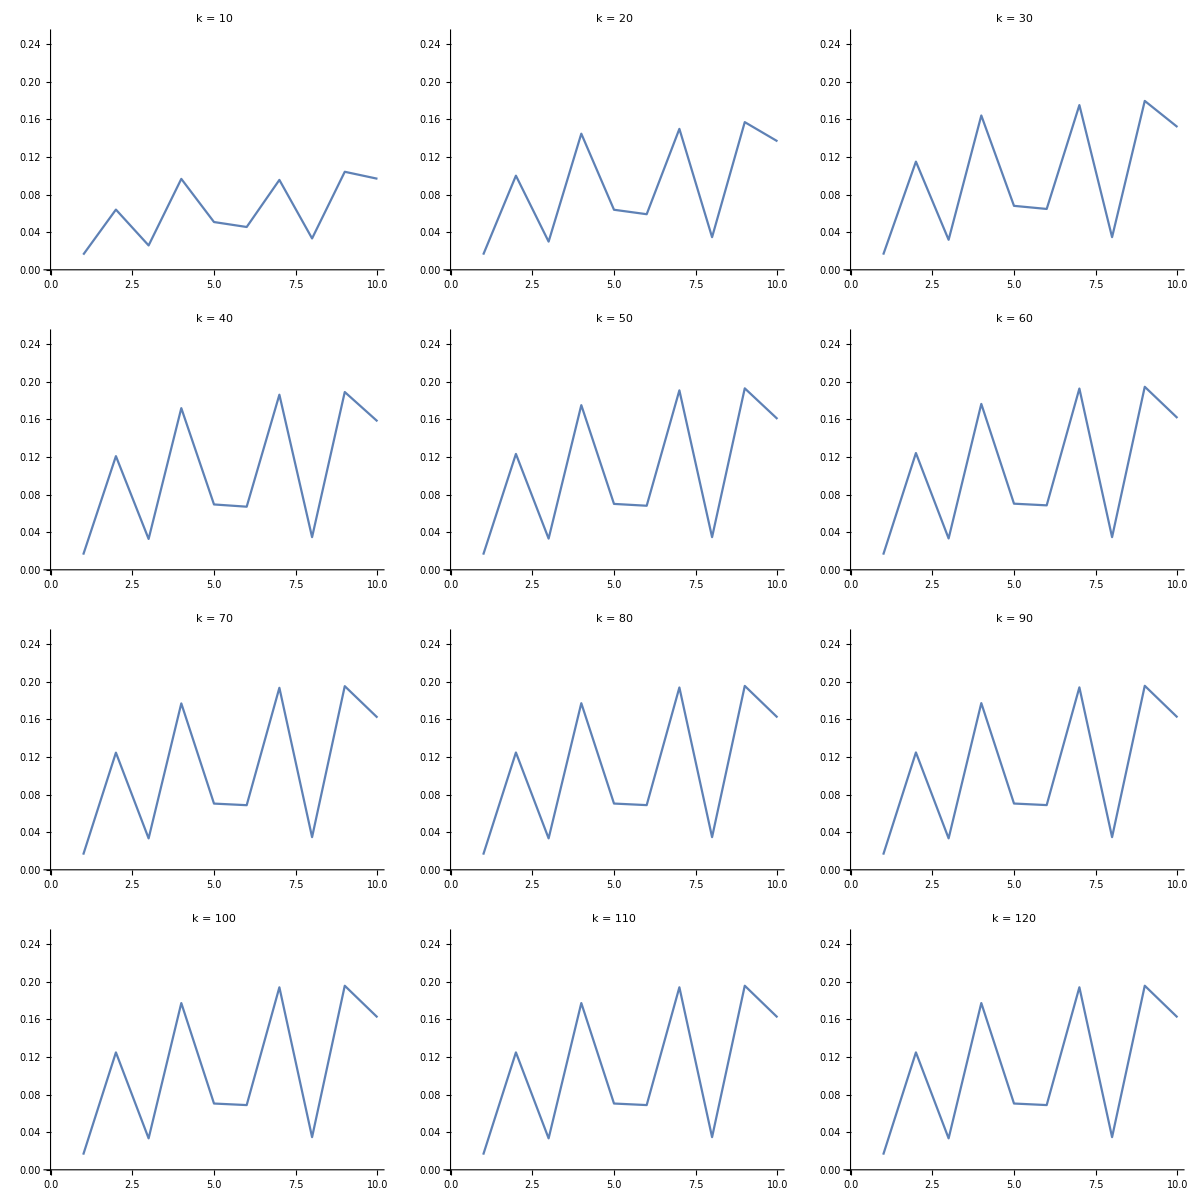

```mathematica
TT=RandomTernaryT[10];Grid[Partition[Table[SetParameters[<|"β"->2.,"μ"->3.,"λ"->1.,"ρ"->0.9,"δ"->0.9,"α"->2.25,"k"->k|>];ListLinePlot[PrinceRank[PowerStructure[Table[1,10],TT]],PlotRange->{0,.25},ImageSize->{125,110},PlotLabel->Caption["k = "<>ToString[k]]],{k,10,120,10}],3]]
```

#### IPR other 2

```mathematica
SetParameters[<|"β"->1.5,"μ"->2,"λ"->1,"ρ"->0.85,"δ"->0.7|>];
ps = PowerStructure[{2},NormalizeTernaryT[{{1}}]];
reel = Part[Map[ShowPowerStructure[#,<|"circular"->True,"size"->{30,20}|>]&,SimulateLawOfMotion[ps]],{1,3,5,7}];
SpacedRow[MapIndexed[AddCaption[#,"t = "<>ToString[First[#2]]]&,reel],40]
```

-Graphics-
t = 1-Graphics-
t = 2-Graphics-
t = 3-Graphics-
t = 4

## Legal Moves

#### Legality - why needed

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.98,"δ"->0.5,"α"->2.25,"k"->20|>];f[x_,cap_]:=With[{ps=PowerStructure[{.2,.8,1},NormalizeTernaryT[x]]},AddCaption[ShowPowerStructure[ps,<|"focal"->{1},"ternary"->True,"circular"->True,"color"->1,"size"->{60,60},"labels"->True|>],StringJoin[{cap,", p_3= "<>ToString[Round[PrinceRank[ps][[3]],.01]]}]]];
SpacedRow[{f[({{0, 0, 0}, {0, 0, -1}, {0, -1, 0}}),"t=1"],f[({{0, 0, 1}, {0, 0, -1}, {1, -1, 0}}),"t=2"]},25]
Clear[f]
```

-Graphics-
t=1, p_3= 0.3-Graphics-
t=2, p_3= 0.28

## Move Selection

#### Principal variation

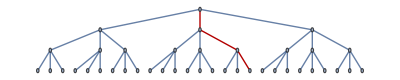

```mathematica
CompleteKaryTree[4,3,
GraphLayout->"LayeredDigraphEmbedding",GraphHighlight->{1<->3,3<->10,10<->31}]
```

## Move Sequences and Distributions

#### Move sequence

```mathematica
ShowMoveSequence[<|"sim"->{<|"s"->{1.,0.2,0.6},"T"->{{0.985,0.015000000000000013,0.015000000000000013},{0.007500000000000007,0.985,0.},{0.007500000000000007,0.,0.985}}|>,<|"s"->{1.,0.19002091575737723,0.6003023964922006},"T"->{{0.985,0.007500000000000007,0.007500000000000007},{0.007500000000000007,0.985,-0.007500000000000007},{0.007500000000000007,-0.007500000000000007,0.985}},"pr"->{0.4928243435524422,0.007672145364298432,0.15982084394937454},"i"->2|>,<|"s"->{0.9999999999999999,0.18608997162200375,0.5661262764758307},"T"->{{0.985,0.007500000000000007,-0.007500000000000007},{0.007500000000000007,0.985,-0.007500000000000007},{-0.007500000000000007,-0.007500000000000007,0.985}},"pr"->{0.542155846156624,0.012096484077451876,0.08488281312881213},"i"->1|>,<|"s"->{1.,0.20926897760352128,0.548502101501545},"T"->{{0.985,0.015000000000000013,-0.015000000000000013},{0.007500000000000007,0.985,0.},{-0.007500000000000007,0.,0.985}},"pr"->{0.49789802997018173,0.03325273499454756,0.09116246713734526},"i"->2|>,<|"s"->{1.,0.22176414049745588,0.4926560870962565},"T"->{{0.985,0.,-0.015000000000000013},{0.,1.,0.},{-0.015000000000000013,0.,0.985}},"pr"->{0.5646687974124436,0.027562964793352032,0.03879408202689062},"i"->1|>,<|"s"->{1.,0.2217965333544384,0.5154922859828535},"T"->{{0.985,0.,0.015000000000000013},{0.,1.,0.},{0.015000000000000013,0.,0.985}},"pr"->{0.49392580491416854,0.016438370657118027,0.1508500200262794},"i"->3|>},"seq"->{0,2,1,2,1,3},"plies"->4,"b"->10,"params"-><|"β"->2.,"μ"->5.,"λ"->0.995,"α"->2.25,"δ"->0.8,"ρ"->0.985,"k"->9,"Δ"->0.3|>|>]
```

-Graphics-
t=0-Graphics-
t=1-Graphics-
t=2-Graphics-
t=3-Graphics-
t=4-Graphics-
t=5

#### Move sequence - simultaneous

```mathematica
SetParameters[<|"β"->1.25,"μ"->3,"λ"->.99,"α"->2.05,"δ"->0.3,"ρ"->0.98,"k"->10|>];ps=RandomTernaryPowerStructure[5,4,.3];
ShowMCTSSimulation[MCTSSimulate[ps,3,100,5]]
```

-Graphics-
t=0-Graphics-
t=1-Graphics-
t=2-Graphics-
t=3-Graphics-
t=4-Graphics-
t=5

#### Move distribution

```mathematica
SetParameters[<|"β"->2,"μ"->5,"λ"->.995,"α"->2.25,"δ"->0.8, "ρ"->0.98,"k"->9,"Δ"->0.05|>];ps=PowerStructure[{1,.8,.8},NamedTHierarchy[3]];
SpacedRow[{
AddCaption[ShowPowerStructure[ps,<|"circular"->True|>],"t=0"],AddCaption[ShowWeightedMoveDistribution[ps,1,3,5,20],"Move distribution at t=1"]
},50]
```

-Graphics-
t=0<|-Graphics-→0.6,-Graphics-→0.2,-Graphics-→0.2|>
Move distribution at t=1